## Introduction:

Mathematical approaches have  become more and more relevant in policing. In the CBS TV series, Numb3rs a mathematician genius helps his FBI agent brother to solve crime using maths. It turns out that much of the maths used in the series is actually relevant for law enforcement . There are many approaches described in the book “The numbers behind Numb3rs” and in the series : One of the most prominent method is geoprofiling.

It turns out that Los Angeles mathematicians work together with the police on a methods called predictive policing, where data and mathematical approaches are being used to direct police officers to locations where there is a high probability of a crime being committed. There has been a substantial drop in crime rates . The mathematician Prof. Andrea Bertozzi is leading the efforts in predictive policing.  There is a video where they discuss a model based on the (near) repeat victimisation theory - which is based on the observation that often the same or similar targets have a higher likelihood of being targeted again. In this project i try to analyse the data from Merseyside police  in order to locate the places in Liverpool where crime rates are high and the types of crimes being committed in those areas.
Here i load the dataset into Mathematica

```mathematica
merseyside=Import["C:\\Autumn\\Mathematica\\Project\\2019-10-merseyside-street.csv"];
```

```mathematica
merseyside[[1;;2]]//Transpose//TableForm
```

Crime ID | 52d3591e08c1a0ed1354280332da0ea50dcc5862d2b59e532822209fad06d250
Month | 2019-10
Reported by | Merseyside Police
Falls within | Merseyside Police
Longitude | -3.06916
Latitude | 53.3143
Location | On or near Chester High Road
LSOA code | E01018537
LSOA name | Cheshire West and Chester 001D
Crime type | Drugs
Last outcome category | Offender given a caution
Context |

I only show one dataset. There are 15523 entries in this particular file. Here, Reverse@SortBy is used to show the tally of the data in descending order. We can now look at the tally of the different crime types:

```mathematica
Reverse@SortBy[Tally[merseyside[[2;;,10]]],Last]//TableForm
```

Violence and sexual offences | 4468
Anti-social behaviour | 3319
Criminal damage and arson | 1605
Public order | 1177
Drugs | 1056
Other theft | 840
Burglary | 743
Vehicle crime | 742
Shoplifting | 712
Theft from the person | 211
Other crime | 211
Bicycle theft | 182
Robbery | 137
Possession of weapons | 120

So violence and sexual offences “top” the list with 4468 entries. The following bar chart visualizes the  tally where we can understand the different crimes reported to the Merseyside police. Here, Reverse@SortBy is used to represent the bar chart in descending order. BarChart makes a bar chart with bar lengths y_1,  y_2, ….

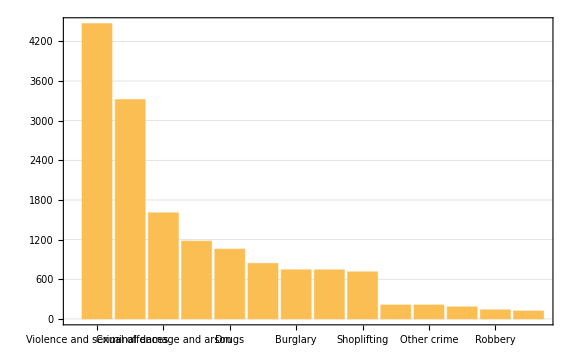

```mathematica
BarChart[(Reverse@SortBy[Tally[merseyside[[2;;,10]]],Last])[[All,2]],ChartLabels->(Rotate[Style[#[[1]],14],Pi/2.]&/@(Reverse@SortBy[Tally[merseyside[[2;;,10]]],Last])),LabelStyle->Directive[Bold,Medium],ImageSize->Large,PlotTheme->"Detailed"]
```

Here, we use Table to generate a list.  We define rules to label the different types of crime:

```mathematica
assignments=Table[(Sort[Tally[merseyside[[2;;,10]]]])[[k,1]]->k,{k,1,Length[Tally[merseyside[[2;;,10]]]]}]
```

{Anti-social behaviour→1,Bicycle theft→2,Burglary→3,Criminal damage and arson→4,Drugs→5,Other crime→6,Other theft→7,Possession of weapons→8,Public order→9,Robbery→10,Shoplifting→11,Theft from the person→12,Vehicle crime→13,Violence and sexual offences→14}

Here, we use select to pick out the elements from the list to plot the types of crimes and  we can then generate a list of locations and types of crime and plot it. This helps the police get an idea about the concentration of crimes around different parts of Liverpool. GeoRegionValuePlot generates a plot in which the geographic regions reg_i are colored according to the values val_i. GeoPosition represents a geodetic position with latitude lat and longitude lon.

```mathematica
crimelocandtype=Select[(merseyside[[2;;,{5,6,10}]]/.assignments),StringQ[#[[1]]]==False&];
GeoRegionValuePlot[GeoPosition[Reverse[{#[[1]],#[[2]]}]]->#[[3]]/Length[assignments]&/@crimelocandtype,ColorFunction->"Rainbow"]
```

-Graphics-

We can also look at particular types of crime and plot that. Here we look at just burglary related crimes reported to the Merseyside Police. Select picks out all elements e_i of list for which crit[e_i] is Truepaclet:ref/True. GeoListPlot generates a map on which the locations loc_i are indicated. GeoPosition represents a geodetic position with latitude lat and longitude lon.

```mathematica
burglaries=Select[crimelocandtype,#[[-1]]==3&];
posBurglaries=GeoListPlot[GeoPosition[Reverse[{#[[1]],#[[2]]}]]&/@burglaries,ImageSize->Large]
```

-Graphics-

We can wrap the above plot into an interactive Manipulate environment. Here we can select the different types of crimes and visualize the concentration of the crime through the plot produced. Manipulate generates a version of expr with controls added to allow interactive manipulation of the value of u. GeoListPlot generates a map on which the locations loc_i are indicated. elect picks out all elements e_i of list for which crit[e_i] is Truepaclet:ref/True.

```mathematica
Manipulate[GeoListPlot[GeoPosition[Reverse[{#[[1]],#[[2]]}]]&/@Select[crimelocandtype,#[[-1]]==assignments[[Position[assignments,k][[1,1]]]][[2]]&],ImageSize->Large],{k,assignments[[All,1]]}]
```

We can of course also calculate the distribution of a particular crime, here burglary. SmoothKernelDistribution represents a smooth kernel distribution based on the data values x_i. ColorReplace finds regions in image whose pixel values are similar to color and replaces them with transparent pixels. ContourPlot generates a contour plot of f as a function of x and y. PDF gives the probability density function for the distribution dist evaluated at x. ImageCompose gives the result of overlaying overlay onto image. ImageResize gives a resized version of image that is width pixels wide. GeoGraphics represents a two-dimensional geographical image. Evaluate causes expr to be evaluated even if it appears as the argument of a function whose attributes specify that it should be held unevaluated.  Flatten is used to flatten out nested lists. Entity represents an entity of specified type identified by name. Here we have generated a heat map where we can see the highest and lowest concentrated areas where burglaries have been reported.

```mathematica
burglaryDistribution=SmoothKernelDistribution[DeleteCases[burglaries[[All,{2,1}]],{"",""}],"SheatherJones"];
cplot=ColorReplace[ContourPlot[PDF[burglaryDistribution,{y,x}],Evaluate@Flatten[{x,{#[[1,1,2]],#[[2,1,2]]}&@(GeoPosition/@Transpose[{{53.0000,53.7405},{-4.1020,-2.1779}}])}],Evaluate@Flatten[{y,{#[[1,1,1]],#[[2,1,1]]}&@(GeoPosition/@Transpose[{{53.0000,53.7405},{-4.1020,-2.1779}}])}],ColorFunction->"Rainbow",Frame->False,PlotRange->All,Contours->405,MaxRecursion->2,ColorFunction->ColorData["TemperatureMap"],PlotRangePadding->0,ContourStyle->None,ImageSize->Full],White->RGBColor[0.4691184586237173,0.10979455248315054,0.5269517756641199]];
ImageCompose[ImageResize[Image[GeoGraphics[Entity["City",{"Liverpool","Liverpool","UnitedKingdom"}],GeoRange->{{53.0000,53.7405},{-4.1020,-2.1779}}]],ImageDimensions@Image[cplot]],{Image[cplot],0.6}]
```

-Graphics-

Alternatively, we can remove very low incident rates.

```mathematica
cplot2=ColorReplace[ContourPlot[PDF[burglaryDistribution,{y,x}],Evaluate@Flatten[{x,{#[[1,1,2]],#[[2,1,2]]}&@(GeoPosition/@Transpose[{{53.0000,53.7405},{-4.1020,-2.1779}}])}],Evaluate@Flatten[{y,{#[[1,1,1]],#[[2,1,1]]}&@(GeoPosition/@Transpose[{{53.0000,53.7405},{-4.1020,-2.1779}}])}],ColorFunction->"Rainbow",Frame->False,PlotRange->All,Contours->405,MaxRecursion->2,ColorFunction->ColorData["TemperatureMap"],PlotRangePadding->0,ContourStyle->None,ImageSize->Large],RGBColor[0.4691184586237173,0.10979455248315054,0.5269517756641199]->White];
ImageCompose[ImageResize[Image[GeoGraphics[Entity["City",{"Liverpool","Liverpool","UnitedKingdom"}],GeoRange->{{53.0000,53.7405},{-4.1020,-2.1779}}]],ImageDimensions@Image[cplot2]],{Image[cplot2],0.6}]
```

-Graphics-

We will now try to add spatial information to the model and thereby try to make it “more similar” to the data. We will use a map of Liverpool as background. Binarize creates a binary image from image by replacing all values above a globally determined threshold with 1 and others with 0. ColorReplace finds regions in image whose pixel values are similar to color and replaces them with transparent pixels. GeoGraphics represents a two-dimensional geographical image. Entity represents an entity of specified type identified by name. GeoRange is an option for GeoGraphicspaclet:ref/GeoGraphics and GeoStylingpaclet:ref/GeoStyling that specifies the range of latitude and longitude to include. ImageSize is an option that specifies the overall size of an image to display for an object. RGBColor specifies opacity a.

```mathematica
backgroundmap=Binarize[ColorReplace[GeoGraphics[Entity["City",{"Liverpool","Liverpool","UnitedKingdom"}],GeoRange->{{53.350,53.500},{-3.100,-2.8779}},ImageSize->Full],RGBColor[0.7645654097466869,0.7601412050621937,0.7438859309145965]->Black],0.5]
```

-Graphics-

## Conclusion:

This project will help the police departments to predict and prevent crimes. We can also take it further and make predictions of the movement of the robbers in the different areas. The police departments will be able to make better policies and better patrolling schedules in the areas which have high crime rates. With more data we can also predict about the timing of the crimes in different locations. This will also help in better police response time. A very similar model can be made for ambulances to reduce their response time. This will also help the police department disperse their special personnel in different areas whenever required. I conclude by saying that this is a small predictive model designed on the basis of Merseyside police departments data. This model predicts the types of crimes being committed in different parts of Liverpool and crime rates in those locations.